# ID2222 Data Mining

# Homework 4: Graph Spectra

## Graph 1

Kim Hammar

KTH Royal Institute of Technology

Konstantin Sozinov

KTH Royal Institute of Technology

## Graph Import

```mathematica
SetDirectory[NotebookDirectory[]];
edgeList = Import["example1.csv","Data"];
graph = Graph[DirectedEdge@@@ edgeList,VertexLabels->"Name"];
```

-Graphics-

## General Graph Properties

### Edge Count

```mathematica
EdgeCount[graph];
```

2196

### Vertex Count

```mathematica
VertexCount[graph];
```

241

### Degree Distribution

```mathematica
Histogram[VertexDegree[graph],{1},"Probability",AxesLabel->{"degree","probability"}];
ListLogLogPlot[GroupBy[VertexDegree[graph], Count], AxesLabel->{"count","degree"}];
```

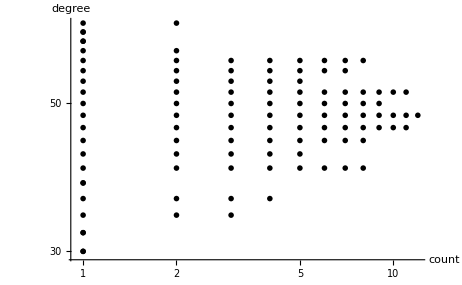

Log-Log plot over degree distribution to do a rough test for powerlaw. Since the distribution is not linear it is probably not a powerlaw.

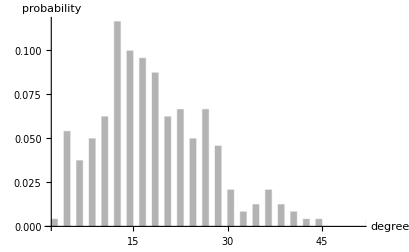

Regular Histogram plot over degree distribution.

### Global Clustering Coefficient

```mathematica
GlobalClusteringCoefficient[graph];
```

1008/4013

## Graph Communities

### Communities Count

```mathematica
Length[FindGraphCommunities[graph]];
```

5

### Communities Plot

```mathematica
CommunityGraphPlot[graph];
```

-Graphics-

## Graph Spectra

### Graph Spectra

```mathematica
A = AdjacencyMatrix[graph];
{eigenVals,eigenVecs} =Eigensystem[N[A]];
```

## Node Centralities

### PageRank Centrality

```mathematica
MaxPageRankCentralNode = VertexList[graph][[Position[PageRankCentrality[graph], 
Max[PageRankCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxPageRankCentralNode];
```

{127}

-Graphics-

### Degree Centrality

```mathematica
MaxDegreeCentralNode = VertexList[graph][[Position[DegreeCentrality[graph], 
Max[DegreeCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxDegreeCentralNode];
```

{127}

-Graphics-

### Closeness Centrality

```mathematica
MaxClosenessCentralityNode = VertexList[graph][[Position[ClosenessCentrality[graph], 
Max[ClosenessCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxClosenessCentralityNode];
```

{127}

-Graphics-

### Betweenness Centrality

```mathematica
MaxBetweenessCentralityNode = VertexList[graph][[Position[BetweennessCentrality[graph], 
Max[BetweennessCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxBetweenessCentralityNode];
```

{15}

-Graphics-

### EigenVector Centrality

```mathematica
MaxEigenVectorCentralityNode = VertexList[graph][[Position[EigenvectorCentrality[graph], 
Max[EigenvectorCentrality[graph]]][[1]]]];
HighlightGraph[graph, MaxEigenVectorCentralityNode];
```

{15}

-Graphics-

### Clustering Coefficient

```mathematica
MaxClusterNode = VertexList[graph][[Position[LocalClusteringCoefficient[graph], 
Max[LocalClusteringCoefficient[graph]]][[1]]]];
HighlightGraph[graph, MaxClusterNode];
```

{95}

-Graphics-

### Adjacency Matrix Heatmap, Non-Normalized Laplacian (Kirchoff), Affinity Matrix

Plotting the heatmap of the adjacency matrix is a common way to visualize a network, it is especially effective when the node partitons are ordered based on node-ids. In our case the partitions are perfectly ordered sequentially on the node ids so the heatmap gives a good indication of the number of clusters.

There exists multiple versions of the Laplacian matrix with small modifications, the Kirchoff matrix is one of them. The affinity matrix is computed as the Jordan Decomposition of the Adjaceny matrix. There are many spectrums that are useful for graph analysis, including the spectrum of the adjacency matrix, the transition matrix and the Laplacian matrix. However, the Laplacian matrix is the most useful for reasoning about the connectivity of the graph as well as its clustering.

```mathematica
MatrixPlot[A];
kirchoffLaplacianMatrix = KirchhoffMatrix[graph];
MatrixPlot[kirchoffLaplacianMatrix];
{affinityMatrix, s} = JordanDecomposition[N[Transpose[A]]];
MatrixPlot[affinityMatrix];
```

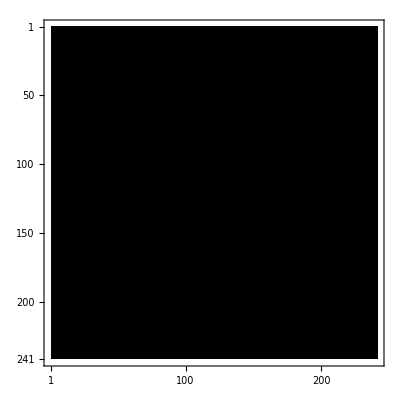

Adjacency Matrix plot

-Graphics-

KirchoffLaplacian Matrix (not normalized)

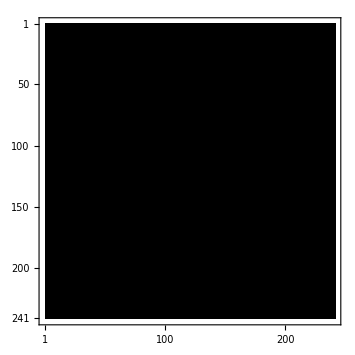

Affinity Matrix Plot

### Degree Matrix, Simple Laplacian

The Degree Matrix D is a diagonal matrix with the degree of each node i on the diagonal (i,i). Here I also compute the simple Laplacian matrix which is L = D - A.

```mathematica
{n,n} = Dimensions[A];
DegreeMatrix = ConstantArray[0, {n,n}];
For[i = 1, i <= n, i++, DegreeMatrix[[i,i]] = Total[A[[i]]]];
MatrixPlot[DegreeMatrix];
simpleLaplacian = DegreeMatrix - A;
MatrixPlot[simpleLaplacian];
```

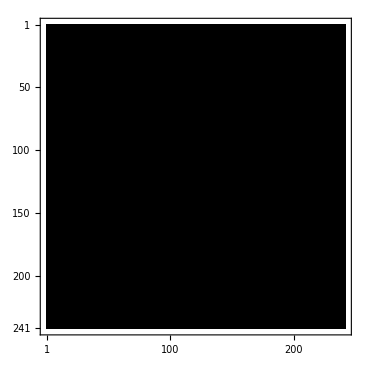

Degree Matrix Plot

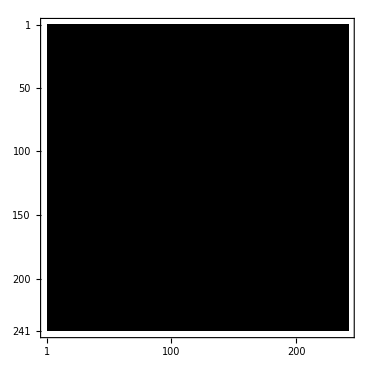

Simple Laplacian Matrix Plot

### EigenGap of Simple Laplacian and Fiedler Vector

In the Laplacian we know that λ_1= 0 with a corresponding eigenvector v_1= [1,...,1]. This follows from the fact that the rows and the columns of the Laplacian sum up to 0 (each row contains number of -1 as number of neighbors plus one entry on the row which is the degree of the node). Further more we can tell by analyzing the higher-order eigenvalues how many connected components the graph has and whether it is a good expander or not. In our case  λ_1 = λ_2 = λ_3 = λ_4 = 0 which means that the graph has 4 connected components. We also know from spectral graph theory that λ_(n ≤ 2)which is in concordance with our results below. Furthermore, by looking at the eigen-gap between λ_4and λ_5we can tell whether it is close or not that there is a fifth disconnected component, and we can see that the fifth components seems to be quite well connected since the eigen-gap is quite large.

Finally, the eigenvector associated with λ_2, also know as the “Fiedler Vector”,  can give a bi-partition of the graph. The Fiedler does not indicate the k-clusters but it can indicate the optimal 2-clusters (and if applied recursively it can even find k clusters, but typically to exploit higher order eigenvectors is a better approach).

```mathematica
{smallestEigenVals, smallestEigenVecs} = Eigensystem[N[simpleLaplacian], -10];
ListPlot[Reverse[Chop[smallestEigenVals]], AxesLabel->{"ith smallest eigenvalue","value"}];
fiedlerVector = smallestEigenVecs[[-2]];
ListLinePlot[Sort[fiedlerVector], AxesLabel->{"node","value in fiedler vector"}];
```

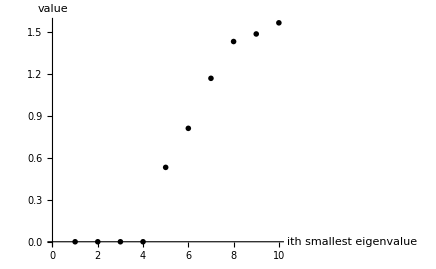

We can see that there is a gap between the 4th smallest eigenvalue and the 5th smallest of the simple Laplacian. This indicates that there are 4 clusters.

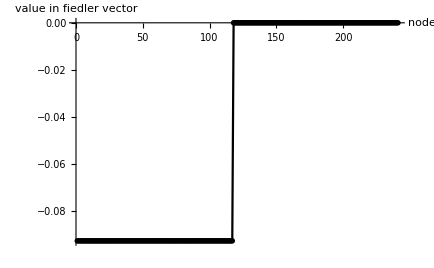

Sorted Fiedler Vector plot, gives a near optimal 2-way partitioning by assigning nodes to partitions based on their index in the Fiedler vector and the sign of the value in the vector.

### Ng, Jordan, & Weiss Laplacian

As mentioned, there are many variants of the laplacian matrix used in different contexts, they all have the same basic characteristics and differ only slightly. In the code snippet below the Laplacian of the Ng, Jordan & Weiss paper is computed as L = D^(-1/2)AD^(-1/2)

```mathematica
k = 4;
{n,n} = Dimensions[A];
njwLaplacian = MatrixPower[DegreeMatrix,-(1/2)].(A.MatrixPower[DegreeMatrix, -(1/2)]);
MatrixPlot[njwLaplacian];
```

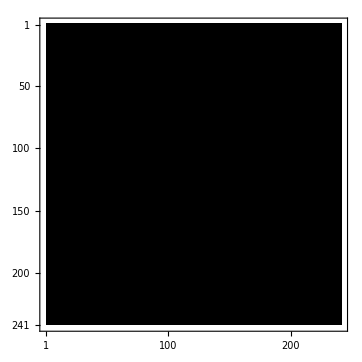

Ng, Jordan, & Weiss Laplacian

### Ng, Jordan, & Weiss Spectral Clustering

Here the bulk of the algorithm in the paper is implemented.

Decide k, we chose k = 4 since this was obvious from the preprocessing, e.g there are 4 connected components for instance.

The eigendecomposition of the Laplacian is computed

X is formed as a matrix with columns being the k largest eigenvectors

Define Y as X with all columns normalized to unit length

Cluster Y with K-means (a row in Y is considered as a datapoint to cluster)

Assign the original datapoints (from the adjacency matrix) to their clusters based on what their corresponding row in Y was clustered as.

```mathematica
k = 4;
{largestEigenVals, largestEigenVecs} = Eigensystem[N[njwLaplacian],4];
X = Transpose[largestEigenVecs];
MatrixPlot[X];
{rows,cols} = Dimensions[X];
Y = ConstantArray[0, {rows,cols}];
For[i = 1, i <= cols, i++, Y[[All,i]] = Normalize[X[[All, i]]]];
clusters = ClusteringComponents[Y,k,1, Method-> "KMeans"];
ListPlot[clusters, AxesLabel->{"node","cluster"}];
```

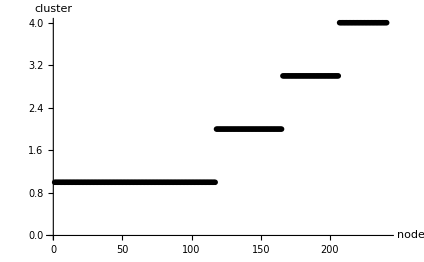

As can be seen from the plot , the 4 clusters found by the spectral clustering are:

Cluster 1: Approximately 0-120

Cluster 2 : Approximately: 120-170

Cluster 3 : Approximately: 170-210

Cluster 4: Approximately: 210 -241

### Test clustering with “wrong” k

```mathematica
k = 3;
clusters = ClusteringComponents[Y,k,1, Method-> "KMeans"];
ListPlot[clusters, AxesLabel->{"node","cluster"}];
k = 2;
clusters = ClusteringComponents[Y,k,1, Method-> "KMeans"];
ListPlot[clusters, AxesLabel->{"node","cluster"}];
k = 5;
clusters = ClusteringComponents[Y,k,1, Method-> "KMeans"];
ListPlot[clusters, AxesLabel->{"node","cluster"}];
k = 6;
clusters = ClusteringComponents[Y,k,1, Method-> "KMeans"];
ListPlot[clusters, AxesLabel->{"node","cluster"}];
```

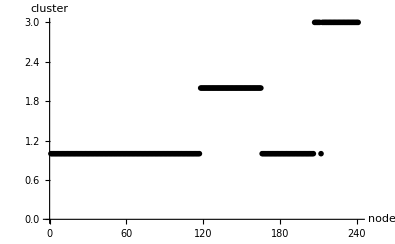

k = 3

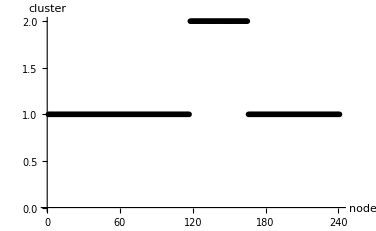

k = 2

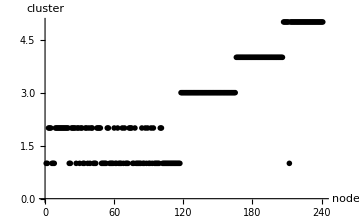

k = 5

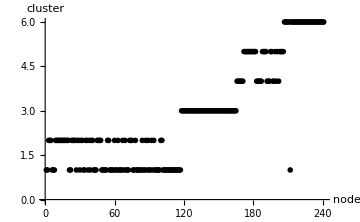

k  = 6